```mathematica
hxhat[m_,kx_,ky_]:=kx/(kx^2+ky^2+m^2)^(1/2)
```

```mathematica
hyhat[m_,kx_,ky_]:=ky/(kx^2+ky^2+m^2)^(1/2)
```

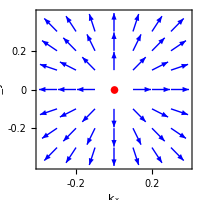

```mathematica
m=0.001;int=0.1;
plot1=Graphics[{Blue,Table[{Arrowheads[0.08(hxhat[m,int i,int j]^2+hyhat[m,int i,int j]^2)^(1/2)],Arrow[{{int i,int j},{int i+0.095hxhat[m,int i,int j],int j+0.095hyhat[m,int i,int j]}}]},{i,-3,3},{j,-3,3}],Red,Disk[{0,0},0.02]},
Frame->True,
FrameLabel->{Style["k_x",15],Style["k_y",15]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{-0.2,0,0.2},None},{{-0.2,0,0.2},None}},
LabelStyle->Directive[14],
ImageSize->200]
```

```mathematica
Export["vortex1.pdf",plot1]
```

vortex1.pdf

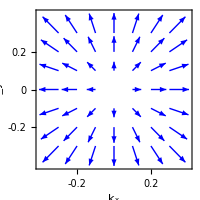

```mathematica
m=0.3;int=0.1;
plot2=Graphics[{Blue,Table[{Arrowheads[0.1(hxhat[m,int i,int j]^2+hyhat[m,int i,int j]^2)^(1/2)],Arrow[{{int i,int j},{int i+0.15hxhat[m,int i,int j],int j+0.15hyhat[m,int i,int j]}}]},{i,-3,3},{j,-3,3}]},
Frame->True,
FrameLabel->{Style["k_x",15],Style["k_y",15]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{-0.2,0,0.2},None},{{-0.2,0,0.2},None}},
LabelStyle->Directive[14],
ImageSize->200]
```

```mathematica
Export["vortex2.pdf",plot2]
```

vortex2.pdf